```mathematica
prep[img_]:=Binarize[Rasterize[img]]
```

```mathematica
Plot[Sin[x],{x,0,5},PlotRange->{0,Automatic}]
```

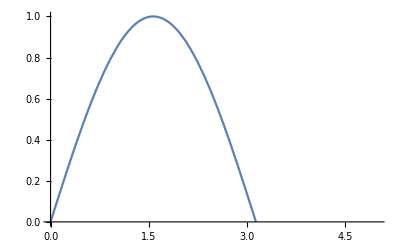
```mathematica
img=Rasterize[-Graphics-];
```

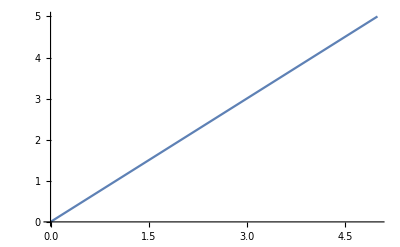
```mathematica
prep[-Graphics-]
```

```mathematica
img=-Graphics-;
```

```mathematica
points={{0,0},{1,1},{5,5}}
```

{{0,0},{1,1},{5,5}}

```mathematica
{o,y,x}={{-0.003872,1.776*^-15},{0.9996,0.9845},{4.998,4.998}}
```

{{-0.003872,1.776×10^-15},{0.9996,0.9845},{4.998,4.998}}


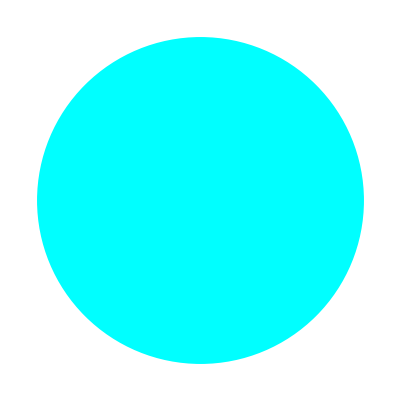
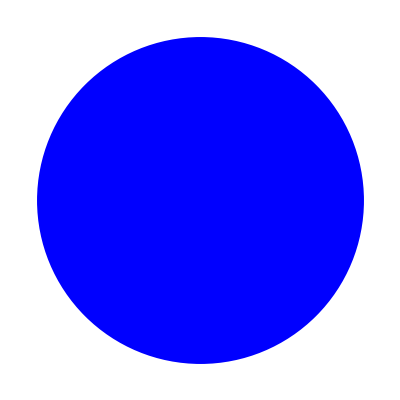
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
data=Round[ImageData[img],1];

col=DeleteDuplicates[Flatten[Round[ImageData[img],1],1]];

Graphics[{RGBColor[#],Disk[]},ImageSize->Tiny]&/@col
```

```mathematica
binImage=Image@Replace[data,{col[[3]]->1,_:>0},{2}];
```

```mathematica
curve=ImageApply[{0,0,0}&,binImage,Masking->ColorNegate[Binarize[GaussianFilter[binImage,5]]]];
```

```mathematica
curvLoc=(Reverse/@Position[ImageData[curve,DataReversed->True],{1.,1.,1.}]);
```

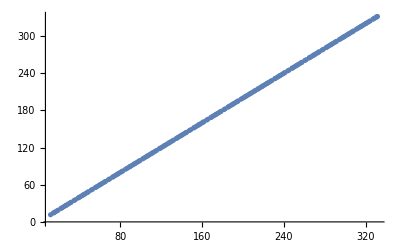

```mathematica
ListPlot[trans@curvLoc,PlotRange->All]
```

```mathematica
lines=ImageLines[Binarize[ColorNegate[img],0.5]]
```

{{{0.,16.2017},{360.,16.2017}},{{18.6359,232.},{19.3999,0.}},{{93.8276,232.},{11.9729,0.}},{{155.076,232.},{233.51,0.}}}

```mathematica
lines=Select[lines,Abs[#[[1,1]]-#[[2,1]]]<2||Abs[#[[1,2]]-#[[2,2]]]<2&]
```

{{{0.,16.2017},{360.,16.2017}},{{18.6359,232.},{19.3999,0.}}}

```mathematica
Show[img,Graphics[{Thick,Orange,Line/@lines}]]
```

-Graphics-

```mathematica
m=(Subtract@@Reverse[#])&/@lines;
minv=DiagonalMatrix[ImageDimensions[img]*{1,-1}].Inverse[Transpose[m]]
orig=ImagePerspectiveTransformation[img,minv,Padding->White]
```

{{1.,0.00329309},{-7.89492×10^-17,1.}}

-Graphics-

```mathematica
mask=Graphics[{Thickness[0.04],Black,Line/@lines},Background->White,PlotRange->Transpose[{{1,1},ImageDimensions[img]}]];
axesFree=ImageMultiply[ColorNegate[img],mask]
```

-Graphics-

```mathematica
axesFreeOrig=ImagePerspectiveTransformation[axesFree,minv,Padding->Black]
comp=MorphologicalComponents[axesFreeOrig];
curve=Thinning[Image[SelectComponents[comp,"Count",-1],"Bit"]]
```

-Graphics-

-Graphics-

```mathematica
points=#[[First@FindCurvePath[#]]]&@Position[Transpose@ImageData[curve,"Bit",DataReversed->True],1];
```

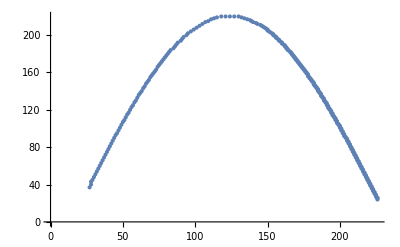

```mathematica
ListPlot[points]
```